# Tutorial on dynamical systems for decision-making

## KSCB 2025 - Based on work by Anastasia Bizyaeva and Alessio Franci - Code (with its bugs) and presentation (with its conceptual mistakes) by Marco Fele

## Identify bifurcation

```mathematica
D[-x+Tanh[u x+0.1],x]
```

-1+u Sech[0.1+u x]^2

First non-zero order is third degree: pitchfork

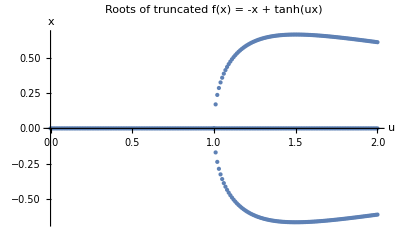

```mathematica
data=Flatten[Table[Module[{poly,roots},poly=Normal[Series[-x+Tanh[u x],{x,0,3}]];
roots=x/. NSolve[poly==0,x,Reals];
Table[{u,r},{r,roots}]],{u,0,2,0.01}],1];

ListPlot[data,PlotStyle->PointSize[Small],AxesLabel->{"u","x"}]
```

Find equilibria as a function of u

```mathematica
equ=Flatten[
Table[
Module[
{roots},
roots=NSolve[-x+Tanh[uP x+0.2]==0,x,Reals];
Table[{u->uP,r}//Flatten,{r,roots}]
],
{uP,0,2,0.001}],
1]
```

{{u→0.,x→0.197375},{u→0.001,x→0.197565},{u→0.002,x→0.197755},{u→0.003,x→0.197946},{u→0.004,x→0.198137},{u→0.005,x→0.198328},3018,{u→1.999,x→-0.203065},{u→1.999,x→0.972958},{u→2.,x→-0.930297},{u→2.,x→-0.202853},{u→2.,x→0.973016}}
 |  |  |  |

Find Jacobian

```mathematica
D[-x+Tanh[u x+0.2],x]
```

-1+u Sech[0.2+u x]^2

Find values of u and x that λ=0

```mathematica
First@OrderingBy[-1+u Sech[0.2+u x]^2 /.equ,Abs]
```

```mathematica
equ[[1489]]
-1+u Sech[0.2+u x]^2 /.equ[[1489]]
```

{u→1.487,x→-0.564598}

0.0129874

Expand system at the critical point

```mathematica
Table[Series[-x+Tanh[u x+0.2],{x,equ[[1489]][[2]]//Values,order}]/.equ[[1489]][[1]],{order,1,5}]//MatrixForm
```

(0.0129874 (x+0.564598)+O[x+0.564598]^2
0.0129874 (x+0.564598)+0.850461 (x+0.564598)^2+O[x+0.564598]^3
0.0129874 (x+0.564598)+0.850461 (x+0.564598)^2-0.0326177 (x+0.564598)^3+O[x+0.564598]^4
0.0129874 (x+0.564598)+0.850461 (x+0.564598)^2-0.0326177 (x+0.564598)^3-0.654222 (x+0.564598)^4+O[x+0.564598]^5
0.0129874 (x+0.564598)+0.850461 (x+0.564598)^2-0.0326177 (x+0.564598)^3-0.654222 (x+0.564598)^4-0.415155 (x+0.564598)^5+O[x+0.564598]^6)

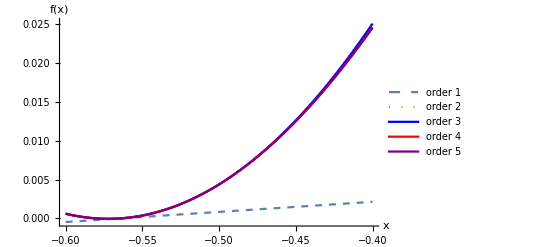

```mathematica
Plot[Evaluate[Normal/@Table[Series[-x+Tanh[u x+0.2],{x,equ[[1489]][[2]]//Values,order}]/. equ[[1489]][[1]],{order,1,5}]],{x,-0.6,-0.4},PlotRange->All,PlotStyle->{Dashed,Dotted,Blue,Red,Purple},PlotLegends->Placed[{"order 1","order 2","order 3","order 4","order 5"},Above],AxesLabel->{"x","f(x)"}]
```

Not very clear, but we can see the first order approximation is close to zero, as the linearization criteria for identifying critical points should be. The next  term (quadratic) exists, so we classify the bifurcation as saddle node

## Unfolding of pitchfork

## Unfolding of pitchfork

```mathematica
D[-x^3+a x^2+p x+b,x]
```

p+2 a x-3 x^2

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"../../outputs/unfolding.csv"}],Prepend[Flatten[Table[Module[{roots},roots=x/. NSolve[-x^3+a x^2+p x+b==0,x,Reals];
Table[{p,a,b,root},{root,roots}]],{p,-2,2,0.01},{b,{0.1,-0.1,0}},{a,{-2,2,0}}],3],{"p","a","b","x"}],"CSV"]
```

C:\Users\marco\Desktop\PhD\KSCB_2025\Code\Mathematica\..\..\outputs\unfolding.csv

## Supercritical

```mathematica
Solve[ -x+Tanh[u x+o]==0,o,Reals]
```

{{o→ConditionalExpression[-u x+ArcTanh[x], -1<x<1]}}

```mathematica
Show[
Plot3D[-u x+ArcTanh[x],
{u, 0, 3},{x,-1.5,1.5},
PlotStyle->Directive[Opacity[0.3],Orange],
AxesLabel->{"Attention u","x^*","Input b"},
Lighting->"Neutral"],
Graphics3D[
{Black,
Thickness[0.01],
Point[
Flatten[Table[With[{xs=SolveValues[Tanh[u x]==x,x,Reals]},Table[{u,xVal,0},{xVal,xs}]],{u,0,3,0.01}],1]
]}
],
Graphics3D[
{Red,
Thickness[0.01],
Point[
Flatten[Table[With[{xs=SolveValues[Tanh[u x+0.5]==x,x,Reals]},Table[{u,xVal,0.5},{xVal,xs}]],{u,0,3,0.01}],1]
]}
],
Graphics3D[
{Blue,
Thickness[0.01],Line[Table[{2,x,Module[{b},SolveValues[-x+Tanh[2 x+b]==0&&-1<x<1,b,Reals][[1]]]},{x,-0.9999,0.9999,0.01}]]}
]
]
```

-Graphics3D-

## Subcritical (closed-loop attention)

```mathematica
Solve[ -x+Tanh[(u0+5 x^2)x+o]==0,o,Reals]
```

{{o→ConditionalExpression[-u0 x-5 x^3+ArcTanh[x], -1<x<1]}}

```mathematica
Show[
Plot3D[-u0 x-4 x^3+ArcTanh[x],
{u0, -4, 4},{x,-1.5,1.5},
PlotStyle->Directive[Opacity[0.3],Orange],
AxesLabel->{"α0","x^*","u"},
Lighting->"Neutral"],
Graphics3D[
{Black,
Thickness[0.01],
Point[
Flatten[Table[With[{xs=SolveValues[Tanh[(u0+4 x^2) x]==x,x,Reals]},Table[{u0,xVal,0},{xVal,xs}]],{u0,-4,4,0.01}],1]
]}
],
Graphics3D[
{Red,
Thickness[0.01],
Point[
Flatten[Table[With[{xs=SolveValues[Tanh[(u0+4 x^2) x+0.5]==x,x,Reals]},Table[{u0,xVal,0.5},{xVal,xs}]],{u0,-4,4,0.01}],1]
]}
],
Graphics3D[
{Blue,
Thickness[0.01],Line[Table[{-1,x,Module[{b},SolveValues[-x+Tanh[(-1+4 x^2) x+b]==0&&-1<x<1,b,Reals][[1]]]},{x,-0.9999,0.9999,0.01}]]}
]
]
```

-Graphics3D-

```mathematica
{ConditionalExpression[Root[-b-p #1-a #1^2+#1^3&,1], ],ConditionalExpression[Root[-b-p #1-a #1^2+#1^3&,2], 2 a^3+27 b+9 a p+2 √((a^2+3 p)^3)>0&&-2 a^3-27 b-9 a p+2 √((a^2+3 p)^3)>0&&a^2+3 p>0],ConditionalExpression[Root[-b-p #1-a #1^2+#1^3&,3], ]}
```

```mathematica
Solve[-x+Tanh[10 x +b]==0,b]
```

{{b→ConditionalExpression[-10 x+ArcTanh[x]+ⅈ π C[1], C[1]∈ℤ]}}

```mathematica
D[-x+Tanh[2 x +b],x]
```

-1+2 Sech[b+2 x]^2

## Separation of timescales

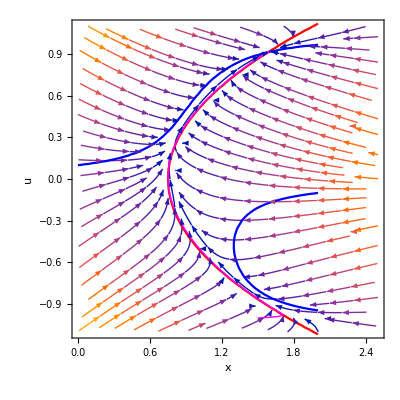

```mathematica
timeSep[d_,u0_,b_,k_,xStart_, uStart_,τ_]:=Module[
{z,us,
nullClines,
rhsx1,rhsu,sol,
gStream},
(* StreamPlot *)
rhsx1=-d x+Tanh[u x+b];
rhsu =-u+u0+k x^2;
gStream=StreamPlot[{ rhsu,rhsx1},{u,0,2.5},{x,-1.1,1.1}];
(*Solution*)
sol=NDSolveValue[
{τ D[u[t],t]==-u[t]+u0+k x[t]^2,
D[x[t],t]==-d x[t]+Tanh[u[t] x[t]+b],
x[0]==xStart,u[0]==uStart},{u[t],x[t]},{t,0,100}];
(* Nullclines*)
nullClines=ContourPlot[
{rhsu==0,
rhsx1==0
},{u,0,2},{x,-2,2},
ContourStyle->{Red,Blue},
ContourShading->False];
Show[gStream,
nullClines,
ParametricPlot[sol,{t,0,100},PlotStyle->{Thick,Magenta}], AxesLabel->{"x","u"},LabelStyle->Directive[Bold,14]
]
]
timeSep[1,0.75,0.1,1,-1,1.5,0.1]
```

## Symmetries in decision-making

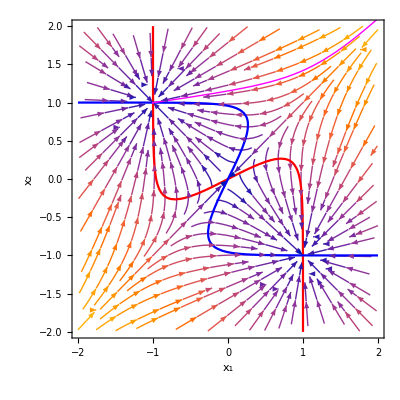

```mathematica
phasePortrait[d_,u_,a1_,a2_,b1_,b2_]:=Module[
{z,us,
nullClines,
rhsx1,rhsx2,sol,
gStream},
(* StreamPlot *)
rhsx1=-d x1+Tanh[u (a1 x1+a2 x2)+b1];
rhsx2 =-d x2+Tanh[u (a1 x2+a2 x1)+b2];
gStream=StreamPlot[{rhsx1, rhsx2},{x1,-2,2},{x2,-2,2}];
(*Solution*)
sol=NDSolveValue[
{D[x1[t],t]==-d x1[t]+Tanh[u (a1 x1[t]+a2 x2[t])+b1],
D[x2[t],t]==-d x2[t]+Tanh[u (a1 x2[t]+a2 x1[t])+b2],
x1[0]==2,x2[0]==2.1},{x1[t],x2[t]},{t,0,100}];
(* Nullclines*)
nullClines=ContourPlot[{rhsx1==0,rhsx2==0},{x1,-2,2},{x2,-2,2},ContourStyle->{Red,Blue},ContourShading->False];
Show[gStream,
nullClines,
ParametricPlot[sol,{t,0,100},PlotStyle->{Thick,Magenta}], AxesLabel->{"x₁","x₂"},LabelStyle->Directive[Bold,14]
]
]
phasePortrait[1,2,1,-1,0,0]
```

Check equivariant criteria for γ=(-1 | 0
0 | -1):

```mathematica
(*Define function vector*)
f={-x1+Tanh[u (a1 x1+a2 x2)],
-x2+Tanh[u (a1 x2+a2 x1)]};
(*Define the transformation matrix and variable vector*)
M={{-1,0},{0,-1}};
vars={x1,x2};
(*Compute transformed variables*)
newVars=M.vars;
(*Criteria*)
Thread[(f/. Thread[vars->newVars])==M.f]//MatrixForm
Thread[(f/. Thread[vars->newVars])==M.f]//Simplify//MatrixForm
```

(x1+Tanh[u (-a1 x1-a2 x2)]==x1-Tanh[u (a1 x1+a2 x2)]
x2+Tanh[u (-a2 x1-a1 x2)]==x2-Tanh[u (a2 x1+a1 x2)])

(True
True)

## Selective ultra-sensitivity in ring attractor

```mathematica
RA[v_,β_,u_,d_,nZ_,init_,bV_,σ_,noiseAuto_,maxTime_,step_,return_]:=Module[
{pi,nGoals,s,(*Useful variables*)
noiseIndex,noiseValues,noiseInterpolation,noiseFunction,(*Noise stuff*)
interactionM,zV,dV,initV,
db,rhs,nlf,
dzdt,sol},
(*Useful variables*)
pi=N[Pi,10];
s[x_,ξ_]:= Tanh[x-ξ]-Tanh[-ξ];(*(Tanh[x-ξ]-Tanh[-ξ])/Sech[ξ]^2*)
(*Noise stuff*)
If[σ>0,
noiseIndex=Table[i/noiseAuto,{i,0,maxTime*noiseAuto}];
noiseValues=Table[
RandomVariate[
NormalDistribution[0, σ], 
maxTime*noiseAuto+1],
{θi, nZ}
];
noiseInterpolation=Table[
Interpolation[
Table[
{noiseIndex[[i]],noiseValues[[θi]][[i]]},
{i,maxTime*noiseAuto+1}
]
],
{θi,nZ}];
noiseFunction =Table[noiseInterpolation[[ϕi]][t],{ϕi,nZ}]];
(*Populate interaction matrix*)
interactionM=Table[
Cos[pi(Abs[Mod[j-i+pi,2pi]-pi]/pi)^v],
{i,-pi,pi,(2pi)/nZ},
{j,-pi,pi,(2pi)/nZ}
][[1;;nZ,1;;nZ]];
If[return  == "kernel",Return[interactionM]];
(*Create bias vector*)
If[return  == "bias",Return[bV]];
(*Create other dynamical variables*)
zV=Table[Subscript[z, i][t],{i,1,nZ}];
initV=Thread[Table[Subscript[z, i][0],{i,1,nZ}]==Table[0,{i, 1, nZ}]];
dV=Table[-d,{i,1,nZ}];
nlf=s[#,β]&/@(u(interactionM.zV/nZ+bV));
If[return  == "nlf",Return[nlf]];
If[σ>0,
rhs=dV*zV+nlf+noiseFunction/nZ,
rhs=dV*zV+nlf
];
If[return  == "rhs",Return[rhs]];
dzdt=Thread[D[zV,t]==rhs];
sol=NDSolveValue[Join[dzdt,init],zV,{t,0,maxTime}];
If[return  == "sol",
Return[sol],
Return[Table[sol/.t->iStep,{iStep, 0, maxTime,step}]]];
]
```

Design input in frequency space

```mathematica
designInput[
mean_,(*signal mean*)
ϕ_,(*phase offset*)
k_,(*Frequency to inject*)
a_,(*Amplitude to inject*)
n_,(*signal lenght*)
σ_,(*noise*)
return_
]:=Module[
{fourierCoef,re,im,output},
(*Step 1:Initialize Fourier coefficients*)
fourierCoef=ConstantArray[0,n];
(*Step 2: Fill positive frequency components (excluding DC and Nyquist)*)
fourierCoef[[1]]=mean;(*Direct current DC, average value, zeroth frequency*)
Do[
re=σ RandomReal[NormalDistribution[]];
im=σ RandomReal[NormalDistribution[]];
fourierCoef[[ki]]=re+I im;(*Always convert from frequency index to mathematica indexing*)
(*Hermitian symmetry: mirror to the negative frequencies. Becuase RA kernel is symmetric*)
fourierCoef[[n-ki+2]]=Conjugate[fourierCoef[[ki]]],(*Indexing just to fill from the back*)
{ki,2,Quotient[n,2]}(* Skip zero frequency and Nyquist (maximum frequency resolution). Will skip one for odd and two for even (even is cleaner becuase of the zeroth frequency). Nyquist has to be real for real valued signal if signal is even*)
];
(*Step 3: Add dominant frequency to chosen harmonic and shift it to chose the bump location*)
fourierCoef[[k+1]]+=a Exp[I k ϕ];
     fourierCoef[[n-(k-1)]]+=Conjugate[fourierCoef[[k+1]]];
(*Step 4:Inverse Fourier Transform to get real-valued signal*)
output=InverseFourier[fourierCoef,FourierParameters->{1,-1}];
If[return == "Fourier",
Return[fourierCoef],
Return[output]]
]
```

Check the properties of the input signals. By designing the input in the frequency domain,  its possible to come up with a multidimensional input which projection in the ultra-sensitive direction (dominant eigenvalues of the kernel) is equal to the amplitude in the first harmonic.  Funky Fourier business to shift the bump location.

```mathematica
nZ=201;
maxEigenV=Table[Exp[(I 2 N[Pi,10]k)/nZ]//Re,{k,0,nZ-1}];
(*vPlus=Table[Cos[(2  N[Pi,10] i)/nZ],{i, 0,nZ-1}]//Normalize;
vMin=Table[Sin[(2 N[Pi,10]i)/nZ],{i, 0,nZ-1}]//Normalize;*)
```

```mathematica
(*Generate 3D point data for both*)
bF1=designInput[0,0,1,1,11,0, "Fourier"];
bF2=designInput[0,-N[Pi,10]/2,1,1,11,0, "Fourier"];
(*Frequency index labeling*)
half=Quotient[11,2];
freqs=Join[Range[0,half],Range[-half,-1]];

data1=Table[{freqs[[k]],Re[bF1[[k]]],Im[bF1[[k]]]},{k,11}];
data2=Table[{freqs[[k]],Re[bF2[[k]]],Im[bF2[[k]]]},{k,11}];
Row[
{ListPointPlot3D[data1,AxesLabel->{"Frequency","Re","Im"},PlotLabel->"Fourier of bV1 (ϕ = 0)",PlotStyle->Blue,BoxRatios->{1,1,1},LabelStyle->Directive[FontSize->12],PlotTheme->"Detailed"],ListPointPlot3D[data2,AxesLabel->{"Frequency","Re","Im"},PlotLabel->"Fourier of bV1 (ϕ = 0)",PlotStyle->Blue,BoxRatios->{1,1,1},LabelStyle->Directive[FontSize->12],PlotTheme->"Detailed"]}
]
```

-Graphics3D--Graphics3D-

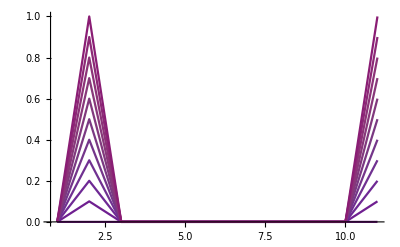

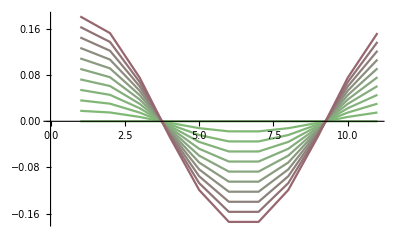

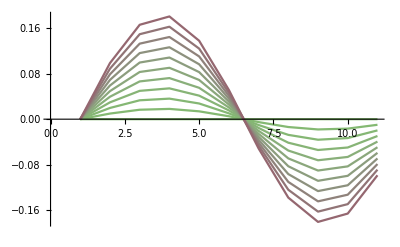

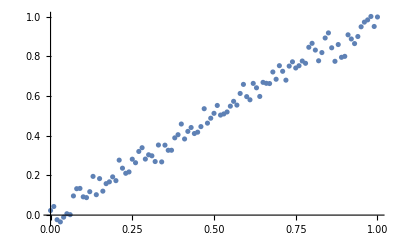

```mathematica
ListPlot[Table[Fourier[designInput[0,0,1,bias,11,0],FourierParameters->{1,-1}],{bias,0,1,0.1}],Joined->True,ColorFunction->"Rainbow",PlotRange->All]
ListPlot[Table[Re[designInput[0,0,1,bias,11,0]],{bias,0,1,0.1}],Joined->True,ColorFunction->"Rainbow"]
ListPlot[Table[Re[designInput[0,-N[Pi,10]/2,1,bias,11,0]],{bias,0,1,0.1}],Joined->True,ColorFunction->"Rainbow"]
ListPlot[Table[{bias,Re[designInput[0,0,1,bias,nZ,0.025]].maxEigenV},{bias,0,1,0.01}]]
```

Create inputs

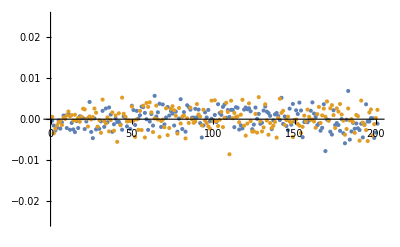

```mathematica
vAlligned=designInput[0,N[Pi,10],1,0.1,nZ,0.025]//Re;
vDisalligned=designInput[0,N[Pi,10],1,0,nZ,0.025]//Re;
ListPlot[{vAlligned,vDisalligned},PlotRange->{-0.025,0.025}]
```

```mathematica
Export[
FileNameJoin[{NotebookDirectory[],"../../outputs/selective_ultrasensitivity/alligned.csv"}],
vAlligned,
"CSV"];
Export[
FileNameJoin[{NotebookDirectory[],"../../outputs/selective_ultrasensitivity/disalligned.csv"}],
vDisalligned,
"CSV"];
```

Feed the inputs to the ring attractor

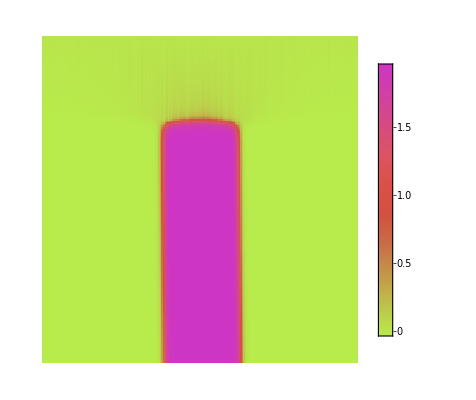

```mathematica
RAalligned = RA[
0.5,(*v*)
2,(*β*)
35,(*u*)
1,(*d*)
nZ,(*nZ*)
{Subscript[z, nZ][0]==0,Thread[Table[Subscript[z, i][0],{i,nZ-1}]==Table[0,{i,nZ-1}]]}//Flatten,
vAlligned,(*{0,Table[0,{i,nZ-1}]}//Flatten,vAlligned*)
0,(*σ*)
1,(*auto*)
100,(*maxtime*)
0.5,(*step*)
"" (*return*)
];
ArrayPlot[
RAalligned,
AspectRatio->1,
ColorFunction->"NeonColors",PlotLegends->Automatic]
```

```mathematica
Export[
FileNameJoin[{NotebookDirectory[],"../../outputs/selective_ultrasensitivity/RA_alligned.csv"}],
RAalligned,
"CSV"];
```

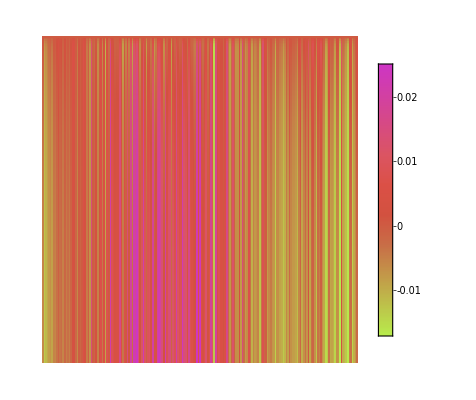

```mathematica
RAdisalligned = RA[
0.5,(*v*)
2,(*β*)
35,(*u*)
1,(*d*)
nZ,(*nZ*)
{Subscript[z, nZ][0]==0,Thread[Table[Subscript[z, i][0],{i,nZ-1}]==Table[0,{i,nZ-1}]]}//Flatten,
vDisalligned,(*{0,Table[0,{i,nZ-1}]}//Flatten,*)
0,(*σ*)
1,(*auto*)
100,(*maxtime*)
0.5,(*step*)
"" (*return*)
];
ArrayPlot[
RAdisalligned,
AspectRatio->1,
ColorFunction->"NeonColors",PlotLegends->Automatic]
```

```mathematica
Export[
FileNameJoin[{NotebookDirectory[],"../../outputs/selective_ultrasensitivity/RA_disalligned.csv"}],
RAdisalligned,
"CSV"];
```

## Play with 3D circulant system to explore selective ultra-sensitivity

```mathematica
C3equivariant[a1_,a2_,a3_,u_,b1_,b2_,b3_,x1start_,x2start_,x3start_]:=Module[
{eqns,sol,A,c1,initialX,bV},
A={{a1,a2,a3},
{a3,a1,a2},
{a2,a3,a1}};
eqns={
x1'[t]==-x1[t]+Tanh[u (a1 x1[t]+a2 x2[t]+a3 x3[t])+b1],
x2'[t]==-x2[t]+Tanh[u (a3 x1[t]+a1 x2[t]+a2 x3[t])+b2],
x3'[t]==-x3[t]+Tanh[u (a2 x1[t]+a3 x2[t]+a1 x3[t])+b3],
x1[0]==x1start,x2[0]==x2start,x3[0]==x3start
};
subSpace[k_,A_]:=Module[
{ρ,n},
n = Length[A];
ρ=Exp[ (2π)/n k];
{Table[Cos[2 π k/n i],{i,0,n-1}],
Table[Sin[2 π k/n i],{i,0,n-1}]}];
c1=Table[Re[Exp[I (2 Pi)/3 k]],{k,0,3-1}];
sol=NDSolveValue[eqns,{x1,x2,x3},{t,0,100}];
(*reduced system*)                                        
bV={b1,b2,b3};
{
Plot[{sol[[1]][t],sol[[2]][t],sol[[3]][t]},{t,0,100},PlotLegends->{"x₁(t)","x₂(t)","x₃(t)"},PlotRange->{-0.2,0.5}
],
Show[
ParametricPlot3D[
{sol[[1]][t],sol[[2]][t],sol[[3]][t]},
{t,0,50},
PlotRange->{{-0.15,0.15},{-0.15,0.15},{-0.15,0.15}},AxesLabel->{"x₁","x₂","x₃"},
PlotStyle->Thick,
Boxed->True,
Mesh->None
],
Graphics3D[
{Red,Arrow[{{0,0,0},bV}],
Black,Arrow[{{0,0,0},c1/10}],
Blue,Arrow[{{0,0,0},bV.c1/(c1.c1)c1}]
}
]
]
}
]
Manipulate[C3equivariant[
a1,a2,a3,
u,
b1,b2,b3,
x1,x2,x3],
{{u,0.5},0,10},
{{a1,1},-5,5},{{a2,-1},-5,5},{{a3,-1},-5,5},
{{x1,0},-1,1},{{x2,0},-1,1},{{x3,0},-1,1},
{{b1,0.1},-1,1},{{b2,0.1},-1,1},{{b3,0.1},-1,1}]
```